# Complex Integration

### Cauchy and Morera Theorems

Theorem 4.2 p96:  f(z) analytic and singularity free on and within a closed contour Γ implies ∮_Γ f(z)dz=0.

Theorem 4.3 p97: f continuous on a domain and ∮_Γ f(z)dz=0 for any closed contour within the domain implies f is analytic on the domain.

### Deforming Contours and Simple Contours

We can deform closed contours round isolated singularities simpler 
to “tiny circles” round singularities joined by “two-way” contours!

A ccw parametrization for a tiny circle around a pole f[z]=r/(z-c)^n is z(t)=c+ϵ E^(2π ⅈ t) with z'[t]=2π ⅈ ϵ E^(2π ⅈ t) is a tiny circle ccw parametrization around a pole f[z]=r/(z-c)^n
	∫_0^1 f[z[t]]*z'[t]dt={ 2π ⅈ r | n=1                    
0 | n=2,3,4,…
The winding number of w(c) for a contour Γ around a point c is the number of times the contour winds around the contour in the ccw direction.  Negative winding numbers indicate clockwise winding.  The winding number of a singularity gives the number of circum-navigations when we shrink contours down to “tiny-circles”.

### Residue Theorem

If a contour Γ encloses an analytic function f(z) with a finite number simple poles c_1,c_2,…,c_m then 
	∫_Γ f(z)dz=2π ⅈ   ∑_(j=1)^m w(c_j) r_j
where the residues r_j=lim_(z→c_j) (z-c_j)f(z) gives the behavior f(z)∼r_j/(z-c_j) for z≈c_j.  
https://en.wikipedia.org/wiki/Residue_theorem

### Practice Example 1

a) Setup Calculus 2 integrals for ∫_Γ f(z)dz where Γ is the edge of the axis aligned square with corners at -2 and 2+2ⅈ.

b) Compute∫_Γ f(z)dz for f(z)=z^2 using part a.

c) Explain how to compute∫_Γ f(z)dz for f(z)=z^2 the easy way.

d) Explain how to compute∫_Γ f(z)dz for f(z)=z^2+(3ⅈ)/(z-ⅈ)+2/(z+ⅈ) the easy way.

### Practice Example 2

a) Setup Calculus 2 integrals for ∫_Γ f(z)dz where Γ is the chunk of the real axis from -2<x<2  closed with the top half semicircle of radius 2.

b) Compute∫_Γ f(z)dz for f(z)=z^2 using part a.

c) Explain how to compute∫_Γ f(z)dz for f(z)=z^2 the easy way.

d) Explain how to compute∫_Γ f(z)dz for f(z)=z^2+(3ⅈ)/(z-ⅈ)+2/(z+ⅈ) the easy way.

### Practice Example 3

Compute ∫_(-∞)^∞ 1/(x^2+4)dx.  Explain all your steps.

### Practice Example 4

Compute ∫_(-∞)^∞ x/((x^2+4)(x^2+2x+2))dx.  Explain all your steps.

We should be able to see fairly fast where the -π/10 is coming from!

```mathematica
Integrate[x/((x^2+4)(x^2+2x +2)),{x, -∞,∞}]
```

-π/10

### Practice Example 5

Outline how to compute ∫_(-∞)^∞ (cos(x))/(x^2+4)dx.  It might help to remember that cos(z)=0.5 (ⅇ^(ⅈ z)+ⅇ^(-ⅈ z))

```mathematica
TabView[{
"ⅇ^ⅈz"->ComplexPlot3D[E^(I z),{z,2}],
"ⅇ^-ⅈz"->ComplexPlot3D[E^(-I z),{z,2}]
}]
```

12

π/(2 ⅇ^2)

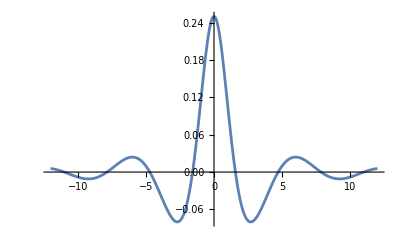

```mathematica
Integrate[Cos[x]/(x^2+4),{x,-∞,∞}]
Plot[Cos[x]/(x^2+4),{x,-12,12},PlotRange->All]
```

### Integration Question

A colleague asked about ∫_-1^1 f(x)dx for the function below.

```mathematica
f[z_]:=(1-z)√(1-z^2)
F[z_]=Integrate[f[z],z]
TabView[{
"f"->ComplexPlot3D[f[z],{z,2},PlotLegends->Automatic],
"F"->ComplexPlot3D[F[z],{z,2},PlotLegends->Automatic]
},2]
```

-1/6 √(1-z^2) (-2-3 z+2 z^2)-ArcTan[(√(1-z^2))/(1+z)]

12

### Interesting Function

There are lots of useful complex functions! Here is an elliptic function
https://en.wikipedia.org/wiki/Elliptic_function
https://en.wikipedia.org/wiki/Jacobi_elliptic_functions

```mathematica
f[z_]:=JacobiSN[z,0.8]
F[z_]=Integrate[f[z],z]
TabView[{
"f"->ComplexPlot3D[f[z],{z,6},PlotLegends->Automatic],
"F"->ComplexPlot3D[F[z],{z,6},PlotLegends->Automatic]
},1]
```

-1.11803 ArcTanh[0.894427 JacobiCD[z,0.8]]

12

```mathematica
?ComplexVectorPlot
```